### Basic Check

is it normalized

```mathematica
FullSimplify[(Sum[(λ^(2(n+m))),{n,0,∞},{m,0,∞}])^2(1-λ^2)^4 ,Assumptions->{λ∈Reals}]
```

1

```mathematica
modeOcc=FullSimplify[(1-λ^2)^2 Sum[n λ^(2(n+m)),{n,0,∞},{m,0,∞}],Assumptions->{λ∈Reals,λ>0}]
```

λ^2/(1-λ^2)

```mathematica
lambdaGivenNanyroot=InverseFunction[modeOcc/.λ->#&]
lambdaGivenN[x_]=Abs[lambdaGivenNanyroot[x]]
SameQ[0.1,modeOcc/.(λ->lambdaGivenN[0.1])]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

-(√#1)/(√(1+#1))&

Abs[(√x)/(√(1+x))]

True

Finding g^(2) using the truncated formula

```mathematica
p1=Simplify[(1-λ^2)^2 Sum[(λ^(n+1)) ,{n,0,∞}]^2]
p2=Simplify[(1-λ^2)^2 Sum[(λ^(n+2)) ,{n,0,∞}]^2]
px=Simplify[(1-λ^2)^2 Sum[(λ^(n+x)) ,{n,0,∞}]^2]
Print["g^2 at low mode occupation P(x)=0 when x>0"]
g2simple=(2 λ^4 (1+λ)^2)/((λ^2 (1+λ)^2+2 λ^4 (1+λ)^2)^2)
g2simple/.{λ->0.01}
Print["g^2 limit at no mode occupancy"]
Limit[g2simple,λ->0]
```

λ^2 (1+λ)^2

λ^4 (1+λ)^2

λ^(2 x) (1+λ)^2

g^2 at low mode occupation P(x)=0 when x>0

(2 λ^4 (1+λ)^2)/((λ^2 (1+λ)^2+2 λ^4 (1+λ)^2)^2)

1.95981

g^2 limit at no mode occupancy

2

```mathematica
g2full=Sum[n(n-1)(px/.{x->n}),{n,0,∞}]/Sum[n(px/.{x->n}),{n,0,∞}]^2
```

-(2 (-1+λ))/(1+λ)

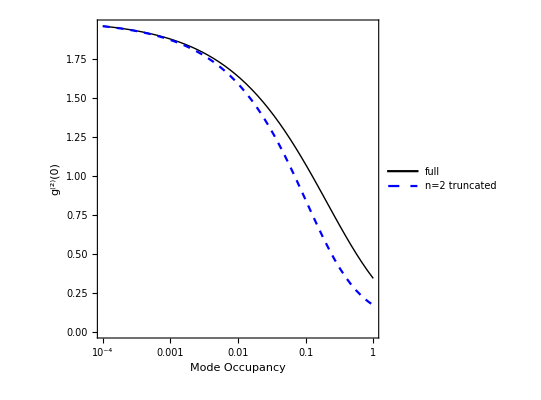

```mathematica
LogLinearPlot[{g2full/.{λ->lambdaGivenN[x]},g2simple/.{λ->Abs[lambdaGivenN[x]]}},{x,1,10^-4},AspectRatio->1,PlotLegends->Placed[{"full","n=2 truncated"},Center],PlotStyle->{{Black,Thick},{Blue,Dashed}},Frame->True,FrameLabel->{"Mode Occupancy","g^(2)(0)"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]
```

## Finding Coincidences

Find the noncoincident output state probability

```mathematica
ProbZeroX=(1-λ^2)Sum[λ^(m+n)1/(Factorial[m]Factorial[n])(1/2)^(m+n)ⅈ^(2m)ⅇ^(ⅈ ϕ(2m))
				Sum[ⅈ^(-j+k)ⅇ^(ⅈ ϕ(-j-k))
					Binomial[m,j]Binomial[n,k]
					√(Factorial[m+n-j-k]Factorial[j+k])
					KroneckerDelta[m+n-j-k]KroneckerDelta[j+k-X]
					,{j,0,n},{k,0,m}]
				Sum[ⅈ^(-a+b)ⅇ^(ⅈ ϕ(a-b))
					Binomial[m,a]Binomial[n,b] 
					√(Factorial[m+n-a-b]Factorial[a+b])
					KroneckerDelta[m+n-a-b]KroneckerDelta[a+b-X] 
					,{a,0,n},{b,0,m}]
,{m,0,∞},{n,0,∞}]
```

$Aborted

```mathematica
Factorial[0]
```

1

```mathematica
Sum[ⅈ^(-j+k)ⅇ^(ⅈ ϕ(-j-k))Binomial[m,j]Binomial[n,k]
					√(Factorial[m+n-j-k]Factorial[j+k])
					KroneckerDelta[m+n-j-k]KroneckerDelta[j+k-X]
					,{j,0,n},{k,0,m}]
```

$Aborted

The simplified version

```mathematica
ProbZeroX=((1-λ^2)(1/2)^X λ^(X)(Factorial[X])ⅈ^(2X)ⅇ^(-2 ⅈ ϕ X) Sum[1/(Factorial[m]Factorial[n])ⅈ^(2m)ⅇ^(ⅈ ϕ(2m))
				Sum[ⅈ^(-2j)
					Binomial[m,j]Binomial[X-m,X-j]
					,{j,0,m}]
				Sum[ⅈ^(-2a)
					Binomial[m,a]Binomial[X-m,X-a]
					,{j,0,X-m}]
,{m,0,X}])^2
```

$Aborted

```mathematica
ⅈ^(-2x)-(-1)^x/.{x->{-1,0,1,2,3,4,5}}
ⅈ^(2x)-(-1)^x/.{x->{-2,-1,0,1,2,3,4,5}}
```

{0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0}

```mathematica
FullSimplify[(-1)^(2m),Assumptions->{m∈Integers}]
```

1

```mathematica
FullSimplify[Binomial[m,j]Binomial[X-m,X-j],Assumptions->Assumptions->{m∈Integers,X∈Integers,j∈Integers}]
```

Binomial[m,j] Binomial[-m+X,-j+X]

```mathematica
Sum[(-1)^j Binomial[m,j]Binomial[X-m,X-j]
					,{j,0,m}]
```

∑_(j=0)^m (-1)^j Binomial[m,j] Binomial[-m+X,-j+X]

```mathematica
numinnersum[y_]:=NSum[(-1)^j Binomial[y,j]Binomial[X-y,X-j]
					,{j,0,y},Method->"AlternatingSigns",PrecisionGoal->30]
numinnersum[10]
```

1.

```mathematica
Table[numinnersum[x]-(-1)^x,{x,0,30}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-4.57001×10^-12,7.02506×10^-11,-8.7832×10^-10,9.07612×10^-9,-7.8543×10^-8,5.7547×10^-7,-3.60273×10^-6}

```mathematica
Simplify[Sum[(-1)^j Binomial[m,j]Binomial[X-m,X-j]
					,{j,0,m-1}]+
Sum[(-1)^j Binomial[m,j]Binomial[X-m,X-j]
					,{j,m,m}],Assumptions->m∈Integers]
```

0

```mathematica
IsOdd[X_]=Piecewise[{{1,Mod[X,2]==1}},0]
Map[IsOdd,{0,1,2,3}]
```

Piecewise[{{1, Mod[X,2]==1}, {0, True}}]

{0,1,0,1}

```mathematica
Sum[(-1)^j(5+j^3),{j,0,X}]/.X->{1,2,3,4,5}
Table[Sum[5+(2j)^3,{j,0,((X-IsOdd[X])/2)}]-Sum[5+(2j+1)^3,{j,0,((X-IsOdd[X])/2)-1+IsOdd[X]  }]/.X-> Y,{Y,{1,2,3,4,5}}]
```

{-1,12,-20,49,-81}

{-1,12,-20,49,-81}

```mathematica
Sum[(-1)^j(5+j^3.2),{j,0,5}]
Sum[5+(2j)^3.2,{j,0,(5-1)/2}]-Sum[5+(2j+1)^3.2,{j,0,((5-1)/2)}]
```

-113.463

-113.463

```mathematica
EvenQ[2]
```

True

```mathematica
Sum[Binomial[m,2j]Binomial[X-m,X-2j]
					,{j,0,m/2}]
Sum[Binomial[m,2j]Binomial[X-m,X-2j]
					,{j,0,(m/2-1) }]
```

1/2 ((1-X)^m+(-1+X)^m) (1-X)^-m

-1+((2-3 m+m^2) Binomial[-m+X,-2+X] (√π Gamma[X]-Gamma[X/2] Gamma[(1+X)/2]))/((-1+X) X Gamma[X/2] Gamma[(1+X)/2])+(-1+m) Binomial[-m+X,-2+X] HypergeometricPFQ[{1-m/2,1-X/2,3/2-X/2},{3/2,2-m/2},1]

```mathematica
Sum[(-1)^m Binomial[m,j]Binomial[X-m,X-j]
					,{j,0,m}]
```

(-1)^m

```mathematica
FullSimplify[ⅈ^(-2x)-(-1)^x,Assumptions->X∈Integers]
```

-2 ⅈ Sin[π x]

```mathematica
({Binomial[-m+X,X]^2 ,Hypergeometric2F1[-m,-X,1-m,-1]^2}
)/.m->1
```

{0,ComplexInfinity}

```mathematica
Sum[1/(Factorial[m]Factorial[X-m])ⅈ^(2m)ⅇ^(ⅈ ϕ(2m))innersum,{m,1,2}]
```

Infinity::indet: Indeterminate expression 0 ⅈ^(2 X) ComplexInfinity encountered.

Indeterminate

```mathematica
ProbZeroX=FullSimplify[(Abs[(1-λ^2)(1/2)^X λ^(X)(Factorial[X])ⅇ^(-2 ⅈ ϕ X) Sum[1/(Factorial[m]Factorial[X-m])(-1)^m ⅇ^(ⅈ ϕ(2m)),{m,0,X}]])^2,Assumptions->{λ∈Reals,X∈Integers,ϕ∈Reals}]
```

4^-X Abs[(λ-ⅇ^(2 ⅈ ϕ) λ)^X (-1+λ^2)]^2

```mathematica
ProbZeroX=4^-X ((λ-ⅇ^(2 ⅈ ϕ) λ)^X (-1+λ^2))((λ-ⅇ^(-2 ⅈ ϕ) λ)^X (-1+λ^2))
```

4^-X (λ-ⅇ^(-2 ⅈ ϕ) λ)^X (λ-ⅇ^(2 ⅈ ϕ) λ)^X (-1+λ^2)^2

```mathematica
ProbClickZero=Sum[ProbZeroX,{X,1,∞}]
ClickNcoProb=(2ProbClickZero+ProbNoAtoms)
ClickNcoProb/.{λ->lambdaGivenN[0.1],ϕ->0.2}
```

-((-1+ⅇ^(2 ⅈ ϕ))^2 λ^2 (-1+λ^2)^2)/(4 ⅇ^(2 ⅈ ϕ)+λ^2-2 ⅇ^(2 ⅈ ϕ) λ^2+ⅇ^(4 ⅈ ϕ) λ^2)

(1-λ^2)^2-(2 (-1+ⅇ^(2 ⅈ ϕ))^2 λ^2 (-1+λ^2)^2)/(4 ⅇ^(2 ⅈ ϕ)+λ^2-2 ⅇ^(2 ⅈ ϕ) λ^2+ⅇ^(4 ⅈ ϕ) λ^2)

0.832398-4.33681×10^-19 ⅈ

```mathematica
ProbNoAtoms=(1-λ^2)^2
```

(1-λ^2)^2

```mathematica
ProbNoAtoms/.λ->0.1
ProbClickZero/.λ->0.1
```

0.9801

-(0.009801 (-1+ⅇ^(2 ⅈ ϕ))^2)/(-3.99-0.02 ⅇ^(2 ⅈ ϕ)+0.01 ⅇ^(4 ⅈ ϕ))

(1-λ^2)^2+2 (-1+λ^2)^2 (BesselI[0,λ]+BesselI[0,2 λ]-2 BesselI[0,√2 λ])

### Non Interfering

```mathematica
probnmDistNM[n_,m_]=((1-λ^2)(λ^(n+m)))^2
probnClickNcoNM[n_,m_]=2*(1/2)^(n+m)
probnClickNcoNMPiece[n_,m_]=Piecewise[{{2*(1/2)^(n+m),n+m≥ 2}},1]
```

λ^(2 m+2 n) (1-λ^2)^2

2^(1-m-n)

Piecewise[{{2^(1-m-n), m+n≥2}, {1, True}}]

```mathematica
ClickNcoProbDista=FullSimplify[Sum[probnmDistNM[n,m]probnClickNcoNMPiece[n,m],{n,0,∞},{m,0,∞}],Assumptions->{λ∈Reals,λ>0}]
ClickNcoProbDistb=FullSimplify[
	Sum[probnmDistNM[n,m]probnClickNcoNM[n,m],{n,1,∞},{m,1,∞}]+
	probnmDistNM[0,0]+
	probnmDistNM[0,1]+
	probnmDistNM[1,0]+
	Sum[probnmDistNM[0,m]probnClickNcoNMPiece[0,m],{m,2,∞}]+
	Sum[probnmDistNM[n,0]probnClickNcoNM[n,0],{n,2,∞}
],Assumptions->{λ∈Reals,λ>0}]
EqualQ[ClickNcoProbDista,ClickNcoProbDistb]
ClickNcoProbDist=ClickNcoProbDista;
ClickNcoProbDist/.λ->0.1
```

-((-1+λ^2)^2 (-4-4 λ^2+λ^4))/((-2+λ^2)^2)

-((-1+λ^2)^2 (-4-4 λ^2+λ^4))/((-2+λ^2)^2)

EqualQ[-((-1+λ^2)^2 (-4-4 λ^2+λ^4))/((-2+λ^2)^2),-((-1+λ^2)^2 (-4-4 λ^2+λ^4))/((-2+λ^2)^2)]

0.99985

### HOM effect Click Click!

```mathematica
HOMClickClickDipVisibility=FullSimplify[((1-ClickNcoProb)-(1-ClickNcoProbDist) )/(1-ClickNcoProb) ,λ>0]
HOMClickClickDipVisibilityPs1orMoreAtoms=FullSimplify[(-(1-(ClickNcoProbDist-ProbNoAtoms))+(1-(ClickNcoProb-ProbNoAtoms)) )/(1-(ClickNcoProb-ProbNoAtoms)) ,λ>0];
```

-(4 (-1+λ^2)^2 (-2+λ^2-2 Cos[2 ϕ]))/((-2+λ^2)^2 (2-λ^4+(2-2 λ^2+λ^4) Cos[2 ϕ]))

```mathematica
Limit[HOMClickClickDipVisibility/.{ϕ-> {0,π/2,π,2π}},λ->0]
```

{1,-1/2,1,1}

0

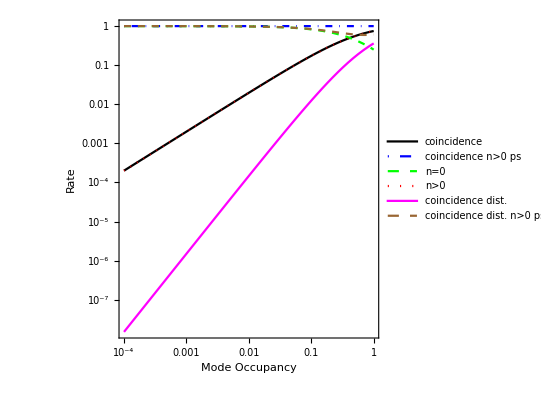

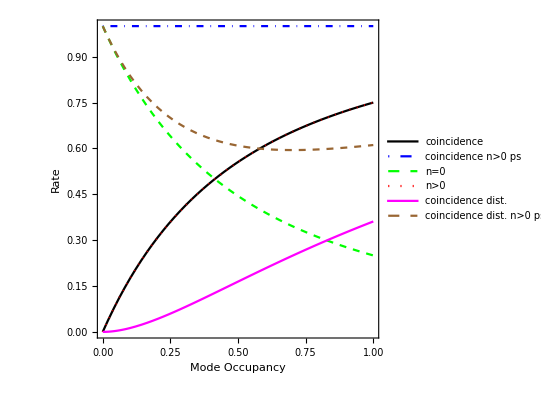

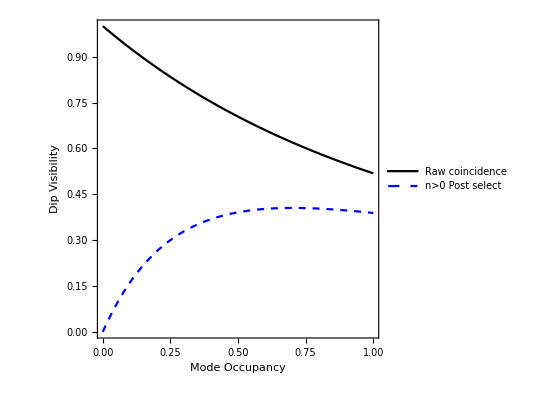

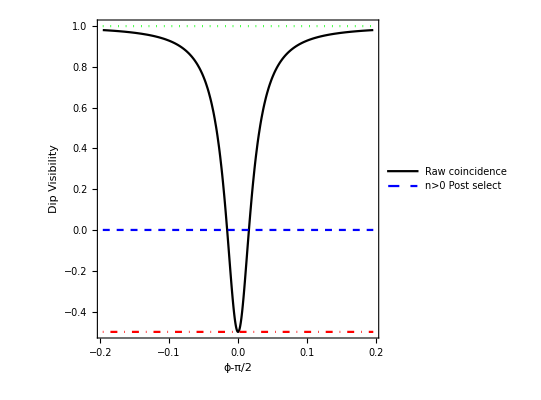

```mathematica
phiTemp=0

LogLogPlot[
{1-ClickNcoProb/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
1-(ClickNcoProb-ProbNoAtoms)/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
ProbNoAtoms/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
1-ProbNoAtoms/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
1-ClickNcoProbDist/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
1-(ClickNcoProbDist-ProbNoAtoms)/.{λ->lambdaGivenN[x],ϕ-> phiTemp}
}
,{x,1,10^-4},AspectRatio->1,PlotLegends->Placed[{"coincidence","coincidence n>0 ps","n=0","n>0 ","coincidence dist.","coincidence dist. n>0 ps"},Top],PlotStyle->{{Black},{Blue,DotDashed},{Green,Dashed},{Red,Dotted},{Magenta},{Brown,Dashed}},
Frame->True,FrameLabel->{"Mode Occupancy","Rate"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]

Plot[
{1-ClickNcoProb/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
1-(ClickNcoProb-ProbNoAtoms)/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
ProbNoAtoms/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
1-ProbNoAtoms/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
1-ClickNcoProbDist/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
1-(ClickNcoProbDist-ProbNoAtoms)/.{λ->lambdaGivenN[x],ϕ-> phiTemp}
}
,{x,1,10^-4},AspectRatio->1,PlotLegends->Placed[{"coincidence","coincidence n>0 ps","n=0","n>0 ","coincidence dist.","coincidence dist. n>0 ps"},Top],PlotStyle->{{Black},{Blue,DotDashed},{Green,Dashed},{Red,Dotted},{Magenta},{Brown,Dashed}},
Frame->True,FrameLabel->{"Mode Occupancy","Rate"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]

Plot[{
HOMClickClickDipVisibility/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
HOMClickClickDipVisibilityPs1orMoreAtoms/.{λ->lambdaGivenN[x],ϕ-> phiTemp}}
,{x,1,10^-6},AspectRatio->1,PlotLegends->Placed[{"Raw coincidence","n>0 Post select"},Top],PlotStyle->{{Black},{Blue,Dashed},{Green,Dotted},{Red,DotDashed}},Frame->True,FrameLabel->{"Mode Occupancy","Dip Visibility"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]
Plot[{
HOMClickClickDipVisibility/.{λ->lambdaGivenN[0.001],ϕ-> ϕplot-π/2},
HOMClickClickDipVisibilityPs1orMoreAtoms/.{λ->lambdaGivenN[0.001],ϕ-> ϕplot-π/2},
1,-0.5}
,{ϕplot,-π/16,+π/16},AspectRatio->1,PlotLegends->Placed[{"Raw coincidence","n>0 Post select"},Top],PlotStyle->{{Black},{Blue,Dashed},{Green,Dotted},{Red,DotDashed}},Frame->True,FrameLabel->{"ϕ-π/2","Dip Visibility"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]
```

```mathematica
HOMClickClickDipVisibilityPs1orMoreAtoms/.{λ->lambdaGivenN[0.001],ϕ-> 0.1}
```

0.00197567

```mathematica
HOMClickClickDipVisibility/.{λ->lambdaGivenN[0.001],ϕ-> 0.1}
```

0.999258+1.45357×10^-6 ⅈ

## Colinear g2

## Postselection

```mathematica
ProbNcoDistNtot=FullSimplify[Sum[probnm[n,m]probncoNM[n,m] KroneckerDelta[n+m-t],{n,1,t},{m,1,t}]+ 2*((1-λ^2)(λ^t))^2 2*(1/2)^t,Assumptions->{λ∈Reals,λ>0,t≥ 2}]
```

2^(1-t) (1+t) λ^(2 t) (-1+λ^2)^2

```mathematica
ProbNcoDistNtot=FullSimplify[Sum[((1-λ^2)(λ^t))^2*2*(1/2)^t,{n,2,t}]+ 2*((1-λ^2)(λ^t))^2 2*(1/2)^t,Assumptions->{λ∈Reals,λ>0,t>0}]
```

2^(1-t) (1+t) λ^(2 t) (-1+λ^2)^2

```mathematica
ProbNcoIndistNtot=2 ( ( 1-λ^2) λ^t)^2
```

2 λ^(2 t) (1-λ^2)^2

```mathematica
visbPostSelNtot=FullSimplify[((1-ProbNcoDistNtot)-(1-ProbNcoIndistNtot))/(1-ProbNcoDistNtot),Assumptions->{λ∈Reals,λ>0,λ<1(*,t>0*)}]
```

-(2 (-1+2^t-t) λ^(2 t) (-1+λ^2)^2)/(-2^t+2 (1+t) λ^(2 t) (-1+λ^2)^2)

```mathematica
visbPostSelNtot/.{t->2,λ->0.5}
```

0.0185567

```mathematica
visbPostSelNtot/.{t->3,λ->Abs[lambdaGivenN[0.9]]}
```

0.0303346

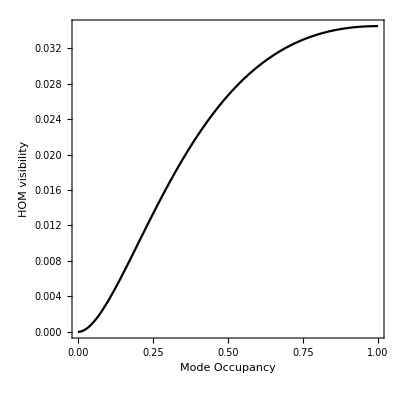

```mathematica
Plot[{visbPostSelNtot/.{λ->Abs[lambdaGivenN[x]],t->2}},{x,1,10^-4},AspectRatio->1,PlotStyle->{{Black},{Blue,DotDashed},{Green,Dashed},{Red,Dotted},{Magenta},{Brown,Dashed}},Frame->True,FrameLabel->{"Mode Occupancy","HOM visibility"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]
```

### Coin flipping

```mathematica
NHeadsChance[n_,h_]=(1/2)^n Binomial[n,h]
```

2^-n Binomial[n,h]

Plot::plln: Limiting value n in {x,0,n} is not a machine-sized real number.

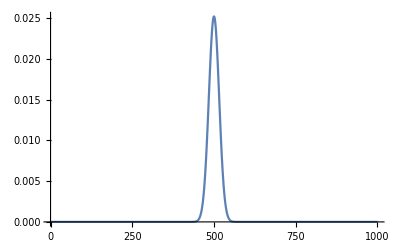

```mathematica
Plot[NHeadsChance[n,x],{x,0,n},PlotRange->All]/.{n->1000}
```